```mathematica
FourierSeries[Clip[Cos[θ],{0,1}],θ,20]
ExpToTrig[%]
N[%]
N[Table[FourierCosCoefficient[Clip[Cos[θ],{0,1}],θ,i],{i,0,20}]]
```

ⅇ^(-ⅈ θ)/4+ⅇ^(ⅈ θ)/4+1/π+ⅇ^(-2 ⅈ θ)/(3 π)+ⅇ^(2 ⅈ θ)/(3 π)-ⅇ^(-4 ⅈ θ)/(15 π)-ⅇ^(4 ⅈ θ)/(15 π)+ⅇ^(-6 ⅈ θ)/(35 π)+ⅇ^(6 ⅈ θ)/(35 π)-ⅇ^(-8 ⅈ θ)/(63 π)-ⅇ^(8 ⅈ θ)/(63 π)+ⅇ^(-10 ⅈ θ)/(99 π)+ⅇ^(10 ⅈ θ)/(99 π)-ⅇ^(-12 ⅈ θ)/(143 π)-ⅇ^(12 ⅈ θ)/(143 π)+ⅇ^(-14 ⅈ θ)/(195 π)+ⅇ^(14 ⅈ θ)/(195 π)-ⅇ^(-16 ⅈ θ)/(255 π)-ⅇ^(16 ⅈ θ)/(255 π)+ⅇ^(-18 ⅈ θ)/(323 π)+ⅇ^(18 ⅈ θ)/(323 π)-ⅇ^(-20 ⅈ θ)/(399 π)-ⅇ^(20 ⅈ θ)/(399 π)

1/π+Cos[θ]/2+(2 Cos[2 θ])/(3 π)-(2 Cos[4 θ])/(15 π)+(2 Cos[6 θ])/(35 π)-(2 Cos[8 θ])/(63 π)+(2 Cos[10 θ])/(99 π)-(2 Cos[12 θ])/(143 π)+(2 Cos[14 θ])/(195 π)-(2 Cos[16 θ])/(255 π)+(2 Cos[18 θ])/(323 π)-(2 Cos[20 θ])/(399 π)

0.31831+0.5 Cos[θ]+0.212207 Cos[2. θ]-0.0424413 Cos[4. θ]+0.0181891 Cos[6. θ]-0.0101051 Cos[8. θ]+0.0064305 Cos[10. θ]-0.00445189 Cos[12. θ]+0.00326472 Cos[14. θ]-0.00249655 Cos[16. θ]+0.00197096 Cos[18. θ]-0.00159554 Cos[20. θ]

{0.63662,0.5,0.212207,0.,-0.0424413,0.,0.0181891,0.,-0.0101051,0.,0.0064305,0.,-0.00445189,0.,0.00326472,0.,-0.00249655,0.,0.00197096,0.,-0.00159554}

```mathematica
FourierSeries[Clip[-Cos[θ],{0,1}],θ,20]
ExpToTrig[%]
N[%]
N[Table[FourierCosCoefficient[Clip[-Cos[θ],{0,1}],θ,i],{i,0,20}]]
```

-1/4 ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)/4+1/π+ⅇ^(-2 ⅈ θ)/(3 π)+ⅇ^(2 ⅈ θ)/(3 π)-ⅇ^(-4 ⅈ θ)/(15 π)-ⅇ^(4 ⅈ θ)/(15 π)+ⅇ^(-6 ⅈ θ)/(35 π)+ⅇ^(6 ⅈ θ)/(35 π)-ⅇ^(-8 ⅈ θ)/(63 π)-ⅇ^(8 ⅈ θ)/(63 π)+ⅇ^(-10 ⅈ θ)/(99 π)+ⅇ^(10 ⅈ θ)/(99 π)-ⅇ^(-12 ⅈ θ)/(143 π)-ⅇ^(12 ⅈ θ)/(143 π)+ⅇ^(-14 ⅈ θ)/(195 π)+ⅇ^(14 ⅈ θ)/(195 π)-ⅇ^(-16 ⅈ θ)/(255 π)-ⅇ^(16 ⅈ θ)/(255 π)+ⅇ^(-18 ⅈ θ)/(323 π)+ⅇ^(18 ⅈ θ)/(323 π)-ⅇ^(-20 ⅈ θ)/(399 π)-ⅇ^(20 ⅈ θ)/(399 π)

1/π-Cos[θ]/2+(2 Cos[2 θ])/(3 π)-(2 Cos[4 θ])/(15 π)+(2 Cos[6 θ])/(35 π)-(2 Cos[8 θ])/(63 π)+(2 Cos[10 θ])/(99 π)-(2 Cos[12 θ])/(143 π)+(2 Cos[14 θ])/(195 π)-(2 Cos[16 θ])/(255 π)+(2 Cos[18 θ])/(323 π)-(2 Cos[20 θ])/(399 π)

0.31831-0.5 Cos[θ]+0.212207 Cos[2. θ]-0.0424413 Cos[4. θ]+0.0181891 Cos[6. θ]-0.0101051 Cos[8. θ]+0.0064305 Cos[10. θ]-0.00445189 Cos[12. θ]+0.00326472 Cos[14. θ]-0.00249655 Cos[16. θ]+0.00197096 Cos[18. θ]-0.00159554 Cos[20. θ]

```mathematica
{0.6366197723675814,-0.5,0.2122065907891938,0.,-0.04244131815783876,0.,0.01818913635335947,0.,-0.010105075751866371,0.,0.006430502751187691,0.,-0.004451886520053017,0.,0.003264716781372212,0.,-0.0024965481269316916,0.,0.0019709590475776514,0.,-0.0015955382766104796}

{0.31831,-0.5,0.212207,0.,-0.0424413,0.,0.0181891,0.,-0.0101051,0.,0.0064305,0.,-0.00445189,0.,0.00326472,0.,-0.00249655,0.,0.00197096,0.,-0.00159554};
```

```mathematica
FourierSeries[Clip[Sin[θ],{0,1}],θ,20]
ExpToTrig[%]
N[%]
N[Table[FourierCosCoefficient[Clip[Sin[θ],{0,1}],θ,i],{i,0,20}]]
```

1/4 ⅈ ⅇ^(-ⅈ θ)-1/4 ⅈ ⅇ^(ⅈ θ)+1/π-ⅇ^(-2 ⅈ θ)/(3 π)-ⅇ^(2 ⅈ θ)/(3 π)-ⅇ^(-4 ⅈ θ)/(15 π)-ⅇ^(4 ⅈ θ)/(15 π)-ⅇ^(-6 ⅈ θ)/(35 π)-ⅇ^(6 ⅈ θ)/(35 π)-ⅇ^(-8 ⅈ θ)/(63 π)-ⅇ^(8 ⅈ θ)/(63 π)-ⅇ^(-10 ⅈ θ)/(99 π)-ⅇ^(10 ⅈ θ)/(99 π)-ⅇ^(-12 ⅈ θ)/(143 π)-ⅇ^(12 ⅈ θ)/(143 π)-ⅇ^(-14 ⅈ θ)/(195 π)-ⅇ^(14 ⅈ θ)/(195 π)-ⅇ^(-16 ⅈ θ)/(255 π)-ⅇ^(16 ⅈ θ)/(255 π)-ⅇ^(-18 ⅈ θ)/(323 π)-ⅇ^(18 ⅈ θ)/(323 π)-ⅇ^(-20 ⅈ θ)/(399 π)-ⅇ^(20 ⅈ θ)/(399 π)

1/π-(2 Cos[2 θ])/(3 π)-(2 Cos[4 θ])/(15 π)-(2 Cos[6 θ])/(35 π)-(2 Cos[8 θ])/(63 π)-(2 Cos[10 θ])/(99 π)-(2 Cos[12 θ])/(143 π)-(2 Cos[14 θ])/(195 π)-(2 Cos[16 θ])/(255 π)-(2 Cos[18 θ])/(323 π)-(2 Cos[20 θ])/(399 π)+Sin[θ]/2

0.31831-0.212207 Cos[2. θ]-0.0424413 Cos[4. θ]-0.0181891 Cos[6. θ]-0.0101051 Cos[8. θ]-0.0064305 Cos[10. θ]-0.00445189 Cos[12. θ]-0.00326472 Cos[14. θ]-0.00249655 Cos[16. θ]-0.00197096 Cos[18. θ]-0.00159554 Cos[20. θ]+0.5 Sin[θ]

{1.27324,0.,-0.424413,0.,-0.0848826,0.,-0.0363783,0.,-0.0202102,0.,-0.012861,0.,-0.00890377,0.,-0.00652943,0.,-0.0049931,0.,-0.00394192,0.,-0.00319108}

```mathematica
FourierSeries[Clip[-Sin[θ],{0,1}],θ,20]
ExpToTrig[%]
N[%]
N[Table[FourierCosCoefficient[Clip[-Sin[θ],{0,1}],θ,i],{i,0,20}]]
```

-1/4 ⅈ ⅇ^(-ⅈ θ)+1/4 ⅈ ⅇ^(ⅈ θ)+1/π-ⅇ^(-2 ⅈ θ)/(3 π)-ⅇ^(2 ⅈ θ)/(3 π)-ⅇ^(-4 ⅈ θ)/(15 π)-ⅇ^(4 ⅈ θ)/(15 π)-ⅇ^(-6 ⅈ θ)/(35 π)-ⅇ^(6 ⅈ θ)/(35 π)-ⅇ^(-8 ⅈ θ)/(63 π)-ⅇ^(8 ⅈ θ)/(63 π)-ⅇ^(-10 ⅈ θ)/(99 π)-ⅇ^(10 ⅈ θ)/(99 π)-ⅇ^(-12 ⅈ θ)/(143 π)-ⅇ^(12 ⅈ θ)/(143 π)-ⅇ^(-14 ⅈ θ)/(195 π)-ⅇ^(14 ⅈ θ)/(195 π)-ⅇ^(-16 ⅈ θ)/(255 π)-ⅇ^(16 ⅈ θ)/(255 π)-ⅇ^(-18 ⅈ θ)/(323 π)-ⅇ^(18 ⅈ θ)/(323 π)-ⅇ^(-20 ⅈ θ)/(399 π)-ⅇ^(20 ⅈ θ)/(399 π)

1/π-(2 Cos[2 θ])/(3 π)-(2 Cos[4 θ])/(15 π)-(2 Cos[6 θ])/(35 π)-(2 Cos[8 θ])/(63 π)-(2 Cos[10 θ])/(99 π)-(2 Cos[12 θ])/(143 π)-(2 Cos[14 θ])/(195 π)-(2 Cos[16 θ])/(255 π)-(2 Cos[18 θ])/(323 π)-(2 Cos[20 θ])/(399 π)-Sin[θ]/2

0.31831-0.212207 Cos[2. θ]-0.0424413 Cos[4. θ]-0.0181891 Cos[6. θ]-0.0101051 Cos[8. θ]-0.0064305 Cos[10. θ]-0.00445189 Cos[12. θ]-0.00326472 Cos[14. θ]-0.00249655 Cos[16. θ]-0.00197096 Cos[18. θ]-0.00159554 Cos[20. θ]-0.5 Sin[θ]

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

Clip[-Cos[θ],{0,1}]+0.5 Clip[-Sin[θ],{0,1}]+0.5 Clip[Sin[θ],{0,1}]

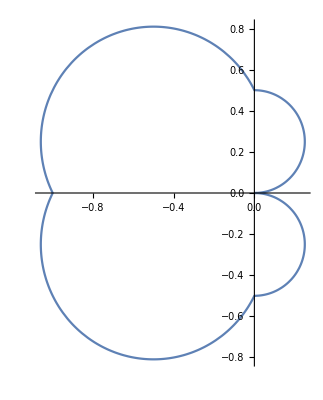

```mathematica
b00=0.5Clip[Sin[θ],{0,1}]+0.5Clip[-Sin[θ],{0,1}]+Clip[-Cos[θ],{0,1}]
PolarPlot[{b00},{θ,0,2Pi}]
```

```mathematica
1/π-(2 Cos[2 θ])/(3 π)-(2 Cos[4 θ])/(15 π)-(2 Cos[6 θ])/(35 π)-(2 Cos[8 θ])/(63 π)-(2 Cos[10 θ])/(99 π)-(2 Cos[12 θ])/(143 π)-(2 Cos[14 θ])/(195 π)-(2 Cos[16 θ])/(255 π)-(2 Cos[18 θ])/(323 π)-(2 Cos[20 θ])/(399 π)+Sin[θ]/2+1/π-(2 Cos[2 θ])/(3 π)-(2 Cos[4 θ])/(15 π)-(2 Cos[6 θ])/(35 π)-(2 Cos[8 θ])/(63 π)-(2 Cos[10 θ])/(99 π)-(2 Cos[12 θ])/(143 π)-(2 Cos[14 θ])/(195 π)-(2 Cos[16 θ])/(255 π)-(2 Cos[18 θ])/(323 π)-(2 Cos[20 θ])/(399 π)+Sin[θ]/2+1/π-(2 Cos[2 θ])/(3 π)-(2 Cos[4 θ])/(15 π)-(2 Cos[6 θ])/(35 π)-(2 Cos[8 θ])/(63 π)-(2 Cos[10 θ])/(99 π)-(2 Cos[12 θ])/(143 π)-(2 Cos[14 θ])/(195 π)-(2 Cos[16 θ])/(255 π)-(2 Cos[18 θ])/(323 π)-(2 Cos[20 θ])/(399 π)-Sin[θ]/2
```

```mathematica
Clip[Cos[θ],{0,1}]
```

Clip[Cos[θ],{0,1}]

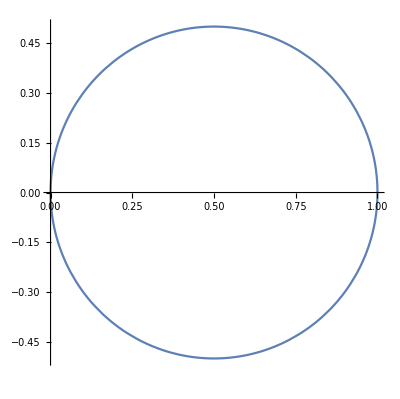

```mathematica
PolarPlot[{%},{θ,0,2Pi}]
```